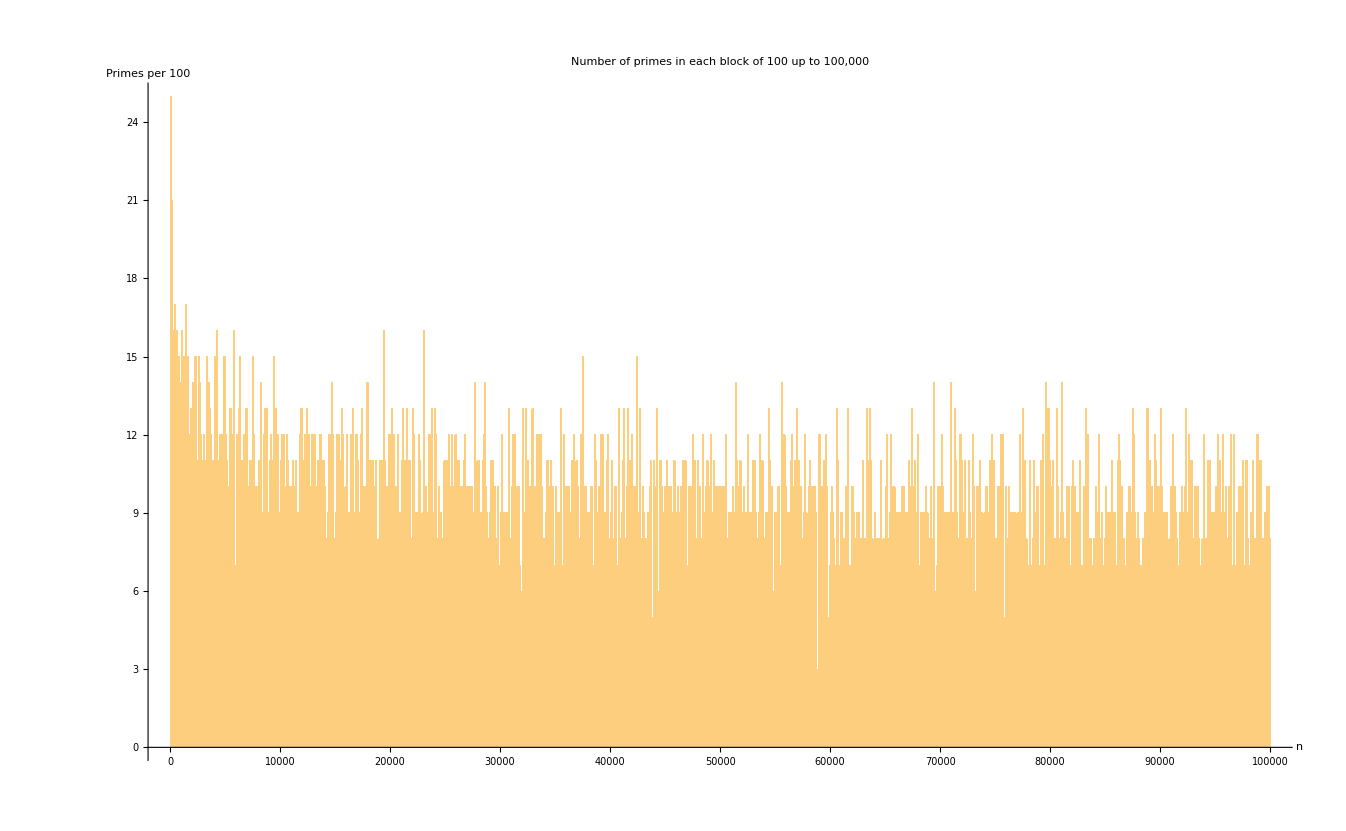

```mathematica
primes=Prime[Range[PrimePi[100000]]];

Histogram[primes,{0,100000,100},AxesLabel->{"n","Primes per 100"},PlotLabel->"Number of primes in each block of 100 up to 100,000",Ticks->{Range[0,100000,10000],Automatic},ImageSize->Large]
```